Initialization of Notebook

```mathematica
ClearAll["Global`*"];ClearSystemCache[];SetDirectory[NotebookDirectory[]];
σx=SparseArray@{{0,1.},{1.,0}};σy=SparseArray@{{0,-I},{I,0}};σz=SparseArray@{{1.,0},{0,-1.}};ide=SparseArray@{{1.,0},{0,1.}};
{sx,sy,sz}=0.5 {σx,σy,σz};
```

Functions

```mathematica
term[op_List,po_List]:=Module[{proxy,swap,result},
proxy=list;
Do[proxy[[po[[i]]]]=op[[i]],{i,1,Length@po}];
swap=proxy[[-1]];
Do[swap=KroneckerProduct[proxy[[i]],swap],{i,-2,-length,-1}];
result=SparseArray@swap;
Return[result];
];
```

Main

```mathematica
dim=2;length=8;hi=0.5;hf=1.0;list=Table[ide,length];ntab=Table[i,{i,1,length}];

Hi=Table[0.,Power[dim,length],Power[dim,length]];
Do[Hi+=term[{-hi σx},{i}],{i,1,length}];
Do[Hi+=term[{-σz,σz},{i,i+1}],{i,1,length-1}];
Hi+=term[{-σz,σz},{1,length}];
{ege,egs}=Eigensystem@Hi;{ege,egs}={ege[[#]],egs[[#]]}&@Ordering[ege][[1]];
Print[ege/length//InputForm]
```

-1.0636352793925343

```mathematica
Hf=Table[0.,Power[dim,length],Power[dim,length]];
Do[Hf+=term[{-hf σx},{i}],{i,1,length}];
Do[Hf+=term[{-σz,σz},{i,i+1}],{i,1,length-1}];
Hf+=term[{-σz,σz},{1,length}];
mx = Table[0.,Power[dim,length],Power[dim,length]];
Do[mx+=term[{σx},{i}],{i,1,length}];
egs=egs//Normalize;
```

```mathematica
wf[t_]:=MatrixExp[-I Hf t].egs;
data=Table[{t/100.,Conjugate[wf[t/100]].mx.wf[t/100]/length//Re},{t,0,400}];
Export["exact_mx_ising8.json",data];
```

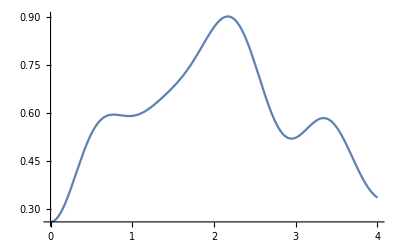

```mathematica
Plot[Conjugate[wf[t]].mx.wf[t]/length,{t,0,4}]
```